Importar y exportar

Todo lo que se ha visto en este libro hasta ahora se ha hecho dentro de Wolfram Language y la base de conocimientos Wolfram. Pero hay ocasiones en que se requiere traer cosas del exterior. Sobra decir que no estarán siempre tan nítidas y organizadas como se acostumbra dentro de Wolfram Language, además de que pueden ser modificadas sin aviso.

Como un primer ejemplo, se importa el texto de la portada del sitio web de la ONU. Para esto se usa la función Import.

Importe la versión en texto de la portada del sitio web de la ONU (podría haber cambiado ya):

```mathematica
Import["http://un.org"]
```

الأمم المتحدة — إنها عالمك  
联合国，您的世界！  
United Nations — It's your world!  
Nations Unies — C'est votre monde!  
Организация Объединенных Наций — это ваш мир!  
Las Naciones Unidas son su mundo

El resultado es una cadena de caracteres, posiblemente con algunas líneas en blanco. Se comienza dividiendo la cadena de caracteres en los cambios de línea.

Se divide en los cambios de línea para obtener una lista de cadenas:

```mathematica
StringSplit[Import["http://un.org"],"\n"]
```

{الأمم المتحدة — إنها عالمك, 联合国，您的世界！,United Nations — It's your world!,Nations Unies — C'est votre monde!,Организация Объединенных Наций — это ваш мир!,Las Naciones Unidas son su mundo}

Identifique la lengua en que está escrita cada una de las cadenas (las líneas en blanco se toman como si fueran inglés):

```mathematica
LanguageIdentify[StringSplit[Import["http://un.org"],"\n"]]
```

{Arabic,Chinese,English,French,Russian,Spanish}

Import se usa para importar una gran variedad de elementos diferentes. "Hyperlinks" trae los hipervínculos que aparecen en una página web; "Images" trae imágenes.

Traiga una lista de los hipervínculos en la portada del sitio web de las NU:

```mathematica
Import["http://un.org","Hyperlinks"]
```

{//www.un.org/ar/index.html,//www.un.org/zh/index.html,//www.un.org/en/index.html,//www.un.org/fr/index.html,//www.un.org/ru/index.html,//www.un.org/es/index.html}

Traiga las imágenes que aparecen en la portada de Wikipedia:

```mathematica
Import["http://wikipedia.org","Images"]
```

{-Graphics-,-Graphics-}

Para ver un ejemplo más sofisticado, se presenta aquí el grafo de los hipervínculos en una porción de mi sitio web. Para mantener un tamaño manejable, se toman solo los 5 primeros hipervínculos en cada nivel, y se ven solo 3 niveles.

Compute una porción del grafo de hipervínculos del sitio web del autor:

```mathematica
NestGraph[Take[Import[#,"Hyperlinks"],5]&,"http://stephenwolfram.com",3]
```

-Graphics-

Wolfram Language puede importar centenares de formatos, incluyendo hojas de cálculo, imágenes, sonidos, geometría, bases de datos, archivos de registro y más. Import se basa automáticamente en la extensión de archivo (.png, .xls, etc.) para determinar de qué se trata.

Importe una foto de mi sitio web:

```mathematica
Import["http://www.stephenwolfram.com/img/homepage/stephen-wolfram-portrait.png"]
```

-Graphics-

¡Wolfram Language me reconoce!

```mathematica
Classify["NotablePerson",%]
```

Stephen Wolfram

De la misma forma que se importan de la web, Import también puede importar de los archivos propios del usuario, ya sea que estén guardados en su computadora o en Wolfram Cloud.

Wolfram Language no solo permite trabajar con páginas web y sus archivos, sino también con servicios o APIs. Por ejemplo, SocialMediaData hace posible traer datos de servicios de medios sociales, al menos cuando se les haya autorizado a enviar sus datos.

Encuentre la red los amigos en Facebook que permiten el acceso a sus datos de conexión:

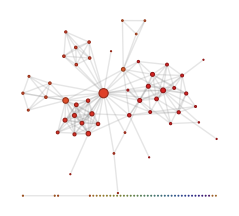

```mathematica
SocialMediaData["Facebook","FriendNetwork"]
```

Otro servicio externo al que se puede acceder con Wolfram Language es la búsqueda en la web.

Busque en la web con las palabras clave “colorful birds” o pájaros de colores vivos:

```mathematica
WebImageSearch["colorful birds"]
```

Dataset[<>]

Solicite miniaturas de las imágenes:

```mathematica
WebImageSearch["colorful birds","Thumbnails"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Se reconocen como tipos diferentes de pájaros:

```mathematica
ImageIdentify/@%
```

{indigo bunting,blue peafowl,mandarin duck,european goldfinch,rainbow lorikeet,ring-necked parakeet,bluebird,rainbow lorikeet,scrub-bird,rainbow lorikeet}

Una fuente muy importante de información externa para su uso en Wolfram Language es el Wolfram Data Repository. La información en este repositorio proviene de muchas partes, pero todo ello está armado de tal manera que se facilite su uso con Wolfram Language.

Se puede ver lo que hay ahí explorando el contenido del Wolfram Data Repository.

-Graphics-

Una vez que se haya localizado alguna cosa que interese, simplemente se usa ResourceData["name"] para traerlo a Wolfram Language.

Obtenga el texto completo de On the Origin of Species, de Darwin, y construya la nube de palabras correspondiente:

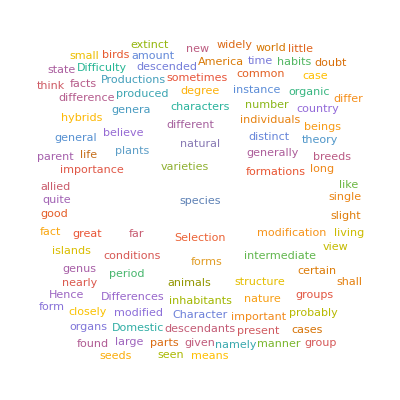

```mathematica
WordCloud[ResourceData["On the Origin of Species"]]
```

Además de traer cosas a Wolfram Language, pueden enviarse al exterior. Por ejemplo, SendMail envía correo electrónico desde Wolfram Language.

Envíe un mensaje a uno mismo por correo electrónico:

```mathematica
SendMail["Hello from the Wolfram Language!"]
```

-Graphics-

Envíe un correo electrónico a una cuenta de prueba, con el asunto “Wolf” y la foto de un lobo adjunta:

```mathematica
SendMail["test@wolfram.com",{"Wolf","Here's a wolf...", -Graphics-}]
```

Cuando se quiere interactuar con programas y servicios externos, se hará necesario muchas veces exportar cosas desde Wolfram Language.

Exporte la gráfica de un círculo a la nube, en formato PDF:

```mathematica
CloudExport[Graphics[Circle[ ]],"PDF"]
```

CloudObject[]

Se puede también exportar a archivos locales usando Export.

Exporte una tabla de primos y sus potencias a un archivo local en hoja de cálculo:

```mathematica
Export["primepowers.xls",Table[Prime[m]^n,{m,10},{n,4}]]
```

primepowers.xls

Aquí está una parte del archivo resultante:

-Graphics-

Importe de regreso el contenido de ese archivo a Wolfram Language:

```mathematica
Import["primepowers.xls"]
```

{{{2.,4.,8.,16.},{3.,9.,27.,81.},{5.,25.,125.,625.},{7.,49.,343.,2401.},{11.,121.,1331.,14641.},{13.,169.,2197.,28561.},{17.,289.,4913.,83521.},{19.,361.,6859.,130321.},{23.,529.,12167.,279841.},{29.,841.,24389.,707281.}}}

Wolfram Language tiene la capacidad para importar y exportar en centenares de formatos de diferente tipo.

Exporte geometría en 3D en un formato adecuado para impresión en 3D:

```mathematica
Export["spikey.stl",LinguisticAssistant["Image"]]
```

spikey.stl

He aquí el resultado de una impresión en 3D del archivo spikey.stl:

-Graphics-

Crear geometría en 3D, en forma apropiada para su impresión, puede ser un asunto bastante complicado. La función Printout3D realiza todos los pasos automáticamente, y puede también enviar la geometría resultante a un servicio de impresión en 3D (o a la impresora 3D propia, si se cuenta con una).

Haga un grupo aleatorio de esferas:

```mathematica
Graphics3D[Sphere[RandomReal[5,{30,3}]]]
```

-Graphics3D-

Envíe esto al servicio Sculpteo para imprimir en 3D:

```mathematica
Printout3D[%,"Sculpteo"]
```

Dataset[<>]

-Graphics- |     | -Graphics-

Vocabulario

Import[lugar] |   | importa desde una ubicación externa lugar
SocialMediaData[...] |   | obtiene información de redes sociales
WebImageSearch["keyword"] |   | hace una búsqueda de imagen en la red
ResourceData["name"] |   | obtiene información del Wolfram Data Repository
SendMail[expr] |   | envía un correo electrónico
CloudExport[expr,format] |   | exporta a la nube en un formato dado
Export[file,expr] |   | exporta a un archivo
Printout3D[source,"service"] |   | envía source a un servicio de impresión 3D

"9 Exercises Available" | "Get Started »"

Importe las imágenes de http://google.com. »

| Sample expected output: |  
  | {-Graphics-,-Graphics-} |

Haga un collage de discos con los colores dominantes en las imágenes de http://google.com. »

| Sample expected output: |  
  | -Graphics- |

Haga una nube de palabras con el texto de http://bbc.co.uk. »

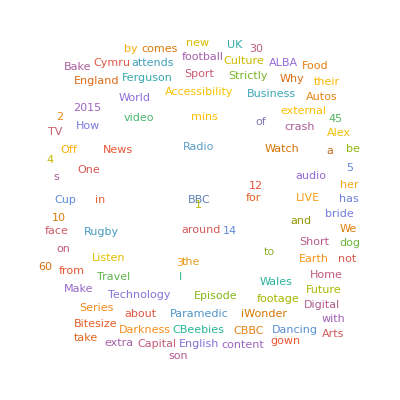
| Sample expected output: |  
  | -Graphics- |

Haga un collage de imágenes con las imágenes en http://nps.gov. »

| Sample expected output: |  
  | -Graphics- |

Use ImageInstanceQ para encontrar fotos de aves en https://en.wikipedia.org/wiki/Ostrich. »

| Sample expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Use TextCases con "Country" para encontrar los casos de nombres de países en http://nato.int, y cree una nube de palabras con ellos. »

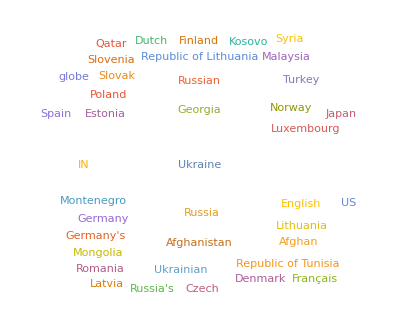
| Sample expected output: |  
  | -Graphics- |

Encuentre el número de vínculos en https://en.wikipedia.org. »

| Sample expected output: |  
  | 292 |

Envíe un mensaje a uno mismo con el mapa de la ubicación donde se encuentre. »

| Sample expected output: |  
  | {"MessageID"→"27542834033679034197.0.WolframLanguage.7Qo3YdBo"} |

Envíe un mensaje a uno mismo con un ícono de la fase actual de la luna. »

| Sample expected output: |  
  | {"MessageID"→"27542858880723918541.0.WolframLanguage.7Qo3YdBo"} |

Preguntas y respuestas

¿Por qué se obtienen resultados diferentes al ejecutar los ejemplos relativos a sitios web?

¡Porque los sitios web han cambiado! Lo que se obtiene es lo que contienen al momento de entrar.

¿Por qué Import no recupera algunos elementos que se ven al visitar una página web con un navegador?

Probablemente porque no están directamente presentes en la fuente HTML de la página web, que es lo que ve Import. Probablemente, se añaden de manera dinámica usando JavaScript.

¿Se puede importar un archivo local desde la computadora si se está usando la nube?

Sí. Use el botón upload  en el sistema en la nube para subir el archivo al sistema propio de archivos en la nube y, luego, use Import.

¿Qué formatos maneja Import?

Vea la lista en wolfr.am/ref-importexport o evalúe $ImportFormats.

¿Cómo determinan Import y Export cuál es el formato que deben usar?

Se puede hacer explícito o, de lo contrario, se determina de las extensiones de los archivos, tales como .gif o .mbox.

¿Dónde pone Export los archivos que crea?

Si no se da el directorio en el nombre del archivo que se especifica, se va al directorio activo. Se puede abrir como lo haría el sistema operativo, usando SystemOpen, y se borra con DeleteFile.

¿Qué es una API?

Es una interfaz de programación de aplicación; una interfaz que un programa expone a otros programas, más que a una persona. Wolfram Language tiene varias APIs, y permite crear las propias mediante el uso de APIFunction.

¿Cómo se autoriza la conexión a una cuenta externa del usuario?

Cuando se usa SocialMediaData o ServiceConnect, por lo regular se pide que se autorice la aplicación Wolfram Connection para ese servicio determinado.

Notas técnicas

ImportString permite que uno “importe” de una cadena de caracteres en lugar de un archivo externo o de un URL. ExportString “exporta” a una cadena de caracteres.

SendMail usa las preferencias de servidor de correo establecidas, o bien un proxy en Wolfram Cloud.

Wolfram Language da soporte a muchos servicios externos. Normalmente usa mecanismos tales como OAuth para autentificarlos.

Otra forma de traer (y enviar) información es mediante la conexión directa de la computadora a un sensor, Arduino, etc. Wolfram Language tiene un marco de trabajo para manejar ese tipo de cosas, incluyendo funciones tales como DeviceReadTimeSeries.

Si se está ejecutando todo en un equipo local, se puede pedir a Wolfram Language la ejecución de programas externos e intercambiar con ellos información usando, por ejemplo, RunProcess. En casos simples se puede simplemente entubar información directamente de un programa, por ejemplo, con Import["!program",...].

Wolfram Language permite lectura y escritura asíncrona de información. Un caso sencillo es URLSubmit, pero ChannelListen, etc. permiten armar un sistema completo de publicación-suscripción manejado externamente.

Para explorar más

Guía para importar y exportar en Wolfram Language »